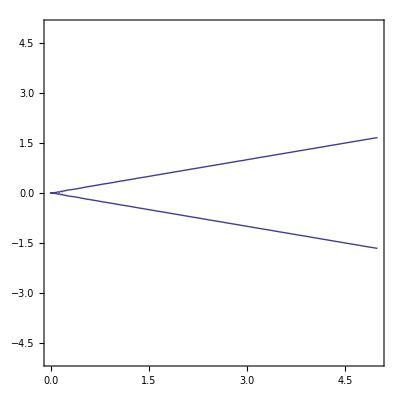

(-0.6 ⅈ w | 3 w
3 w | 0.6 ⅈ w)

```mathematica
ClearAll["Global`*"]
epi:=3
mu:=3
r:=.6
i:=I
b:=2*Pi
H1:={k,w*mu};
H2:={w*epi,k};
H:={H1,H2};
H//MatrixForm;
a:=Det[H]
Factor[Det[H]];
ContourPlot[a==0,{k,0,5},{w,-5,5}]
M1:={-i w r, w mu}
M2:={w epi ,i w r}
M:={M1,M2}
M//MatrixForm
e:=Det[M]
Plot[e==0,{w,0,2}];(*the firse equ*)
```